## initial

```mathematica
ass=Assumptions->{kx,ky,kz,k,θ,χ,ϕ,θp,ϕp,kp,vter,vter,cq,vf,B,μ,chi,fac} ∈ Reals && k>0 && kp>0 && 0<=θ<=π && 0<=θp<=π && βtra>0 && βter>0 && cq>=0 && vf>0 && B>0;
```

```mathematica
Clear[kf1,B,ifun];

kf1[μ_,vf_,cq_,B_,θ_,chi_]:=Block[{e=1},

1/(6 cq)(-2+((-8 vf^3-36 cq vf^2 μ-54 B chi cq^2 e vf^3 Cos[θ]+4 vf^(3/2) √(-4 (vf+3 cq μ)^3+vf (2 vf+9 cq μ+27/2 B chi cq^2 e vf Cos[θ])^2))^(1/3))/vf+(2 2^(2/3) (vf+3 cq μ))/(-18 cq vf^2 μ-vf^3 (4+27 B chi cq^2 e Cos[θ])+3 √3 cq √(vf^3) √(-4 μ^2 (vf+4 cq μ)+B chi e vf^2 Cos[θ] (8 vf+36 cq μ+27 B chi cq^2 e vf Cos[θ])))^(1/3))
];


ifun[μ_,vf_,cq_,B_,chi_]:=Block[{e=1,θ,kfvals,dat,len,i,list},
kfvals[θ_]=1/(6 cq)(-2+((-8 vf^3-36 cq vf^2 μ-54 B chi cq^2 e vf^3 Cos[θ]+4 vf^(3/2) √(-4 (vf+3 cq μ)^3+vf (2 vf+9 cq μ+27/2 B chi cq^2 e vf Cos[θ])^2))^(1/3))/vf+(2 2^(2/3) (vf+3 cq μ))/(-18 cq vf^2 μ-vf^3 (4+27 B chi cq^2 e Cos[θ])+3 √3 cq √(vf^3) √(-4 μ^2 (vf+4 cq μ)+B chi e vf^2 Cos[θ] (8 vf+36 cq μ+27 B chi cq^2 e vf Cos[θ])))^(1/3));
dat=Table[{θ,kfvals[θ]//Chop},{θ,0,π,π/20}];
len=Length[dat];
list=Table[{dat[[i,1]]+dat[[len,1]]+π/20,dat[[len-i,2]] },{i,1,len-1}];
dat=Join[dat,list];
Interpolation[dat,PeriodicInterpolation->True]
];
ifun[mu,vfval,cqval,100,1]
```

InterpolatingFunction[…]

## test

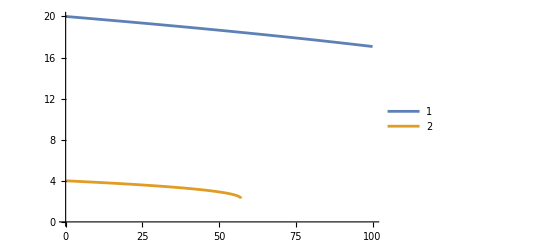

```mathematica
rep={μ->0.1,cq->1,vf->0.005,θ->0,chi->1,e->1};Plot[{(μ+√(μ^2-2 B  Cos[θ] vf^2))/(2 vf)/.rep,(*(μ+√(μ^2-2 B  Cos[θ] vf^2))/(2 vf)-(μ^2 cq)/vf^2/.rep,*)1/(6 cq)(-2+((-8 vf^3-36 cq vf^2 μ-54 B chi cq^2 e vf^3 Cos[θ]+4 vf^(3/2) √(-4 (vf+3 cq μ)^3+vf (2 vf+9 cq μ+27/2 B chi cq^2 e vf Cos[θ])^2))^(1/3))/vf+(2 2^(2/3) (vf+3 cq μ))/(-18 cq vf^2 μ-vf^3 (4+27 B chi cq^2 e Cos[θ])+3 √3 cq √(vf^3) √(-4 μ^2 (vf+4 cq μ)+B chi e vf^2 Cos[θ] (8 vf+36 cq μ+27 B chi cq^2 e vf Cos[θ])))^(1/3))/.rep},{B,0,100},PlotLegends->Automatic]
```

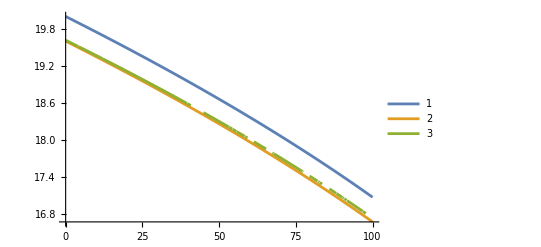

```mathematica
rep={μ->0.1,cq->0.001,vf->0.005,θ->0,chi->1,e->1};Plot[{(μ+√(μ^2-2 B  Cos[θ] vf^2))/(2 vf)/.rep,(μ+√(μ^2-2 B  Cos[θ] vf^2))/(2 vf)-(μ^2 cq)/vf^2/.rep,1/(6 cq)(-2+((-8 vf^3-36 cq vf^2 μ-54 B chi cq^2 e vf^3 Cos[θ]+4 vf^(3/2) √(-4 (vf+3 cq μ)^3+vf (2 vf+9 cq μ+27/2 B chi cq^2 e vf Cos[θ])^2))^(1/3))/vf+(2 2^(2/3) (vf+3 cq μ))/(-18 cq vf^2 μ-vf^3 (4+27 B chi cq^2 e Cos[θ])+3 √3 cq √(vf^3) √(-4 μ^2 (vf+4 cq μ)+B chi e vf^2 Cos[θ] (8 vf+36 cq μ+27 B chi cq^2 e vf Cos[θ])))^(1/3))/.rep},{B,0,100},PlotLegends->Automatic]
```

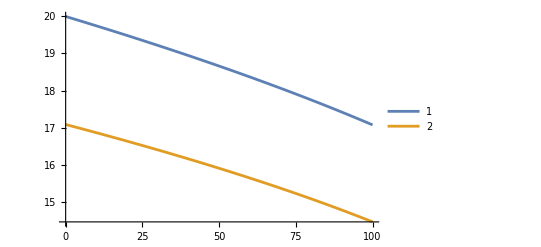

```mathematica
rep={μ->0.1,cq->0.01,vf->0.005,θ->0,chi->1,e->1};Plot[{(μ+√(μ^2-2chi  B  Cos[θ] vf^2))/(2 vf)/.rep,(*(μ+√(μ^2-2 vhi B  Cos[θ] vf^2))/(2 vf)-(μ^2 cq)/vf^2/.rep,*)1/(6 cq)(-2+((-8 vf^3-36 cq vf^2 μ-54 B chi cq^2 e vf^3 Cos[θ]+4 vf^(3/2) √(-4 (vf+3 cq μ)^3+vf (2 vf+9 cq μ+27/2 B chi cq^2 e vf Cos[θ])^2))^(1/3))/vf+(2 2^(2/3) (vf+3 cq μ))/(-18 cq vf^2 μ-vf^3 (4+27 B chi cq^2 e Cos[θ])+3 √3 cq √(vf^3) √(-4 μ^2 (vf+4 cq μ)+B chi e vf^2 Cos[θ] (8 vf+36 cq μ+27 B chi cq^2 e vf Cos[θ])))^(1/3))/.rep},{B,0,100},PlotLegends->Automatic]
```

## Matrix forms

```mathematica
Clear[G];G[χ_, η_,sχ_,sη_]=KroneckerDelta[χ ,η]KroneckerDelta[sχ ,1]KroneckerDelta[sη ,1](ct4 ctp4+st4 stp4+(st2 stp2)/4)+KroneckerDelta[-χ, η]KroneckerDelta[sχ ,1]KroneckerDelta[sη ,1](st4 ctp4+ct4 stp4+(st2 stp2)/4);
G[1,-1,1,1]
```

ctp4 st4+(st2 stp2)/4+ct4 stp4

```mathematica
Clear[eq,Λ11byτ,Λ21byτ,Λ10byτ,Λ20byτ,lhs1,lhs2,lhs3,lhs4,rhs1,rhs2,rhs3,rhs4,λ,a,b,h11,h21,h10,c11,eqn1,eqn2,eqn3,eqn4,eqn5,eqn6,eqn7,eqn8,eqn9,eqn10,eqn11];
Λ11byτ=(-h11+a11 ct4(* Cos[θ/2]^4 *)+b11 st4(* Sin[θ/2]^4 *)+c11 st2(* Sin[θ]^2*));
Λ21byτ=(-h21+a21 ct4+b21 st4+c21 st2);

(* -Graphics- ; -Graphics-*)
lhs1=a11 ct4+b11 st4+c11 st2;     lhs2=a21 ct4+b21 st4+c21 st2;
rhs1=tra11 intθpf11 G[1,1,1,1](-h11+a11 ctp4+b11 stp4+c11 stp2)+ter11 intθpf21 G[1,-1,1,1](-h21+a21 ctp4+b21 stp4+c21 stp2);

rhs2=tra11 intθpf21 G[-1,-1,1,1](-h21+a21 ctp4+b21 stp4+c21 stp2)+ter11 intθpf11 G[-1,1,1,1](-h11+a11 ctp4+b11 stp4+c11 stp2);


eq=lhs1-rhs1;
eqn1=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,0}]//FullSimplify;
eqn2=SeriesCoefficient[eq,{ct4,0,1},{st4,0,0},{st2,0,0}]//FullSimplify;
eqn3=SeriesCoefficient[eq,{ct4,0,0},{st4,0,1},{st2,0,0}]//FullSimplify;
eqn4=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,1}]//FullSimplify;
eq==eqn1+eqn2 ct4+eqn3 st4+ eqn4 st2//FullSimplify

eq=lhs2-rhs2;
eqn5=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,0}]//FullSimplify;
eqn6=SeriesCoefficient[eq,{ct4,0,1},{st4,0,0},{st2,0,0}]//FullSimplify;
eqn7=SeriesCoefficient[eq,{ct4,0,0},{st4,0,1},{st2,0,0}]//FullSimplify;
eqn8=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,1}]//FullSimplify;
eq==eqn5+eqn6 ct4+eqn7 st4+ eqn8 st2//FullSimplify


(* Print["charge consvn:"];*)
intθf11 Λ11byτ+intθf21 Λ21byτ
```

True

True

intθf11 (a11 ct4-h11+c11 st2+b11 st4)+intθf21 (a21 ct4-h21+c21 st2+b21 st4)

```mathematica
Clear[arr,array,array1,cmat];arr=CoefficientArrays[{eqn2==0,eqn3==0,eqn4==0,eqn6==0,eqn7==0,eqn8==0},{a11,b11,c11,a21,b21,c21}];
array=Normal[arr]//Simplify;
cmat=array[[2]]//Simplify;
rep={intθpf11->af11,intθpf21->af21,intθpf10->af10,intθpf20->af20,ctp4->ct4,stp4->st4,stp2->st2,ctp2->ct2};
cmat=Expand[cmat/.rep];
array[[1]]=Expand[array[[1]]/.rep];
rep1={af10 ct2^3->ct2ct2ct210,af20 ct2^3->ct2ct2ct220,af10 ct2^2 st2->ct2ct2at210,af20 ct2^2 st2->ct2ct2at220,af10 ct2 st2->ct2st210,af10 ct2^2->ct2ct210,af20 ct2 st2->ct2st220,af20 ct2^2->ct2ct220,af20 st2^2->st2st220,af10 st2^2->st2st210,af20 h20 st2->hst220,af10 h10 st2->hst210,af10 ct2 h10->hct210,af20 ct2 h20->hct220,
(***********)af20 ct2->ct220,af10 ct2->ct210, af10->zero10,af20->zero20,(**************************)af21 h21 st2->hst221,af21 h21 st4->hst421,af11 ct4 h11->hct411,af21 ct4 h21->hct421,af11 h11 st4->hst411,af11 h11 st2->hst211,af10 h10->hzero10,af20 h20->hzero20,(**************)af11 ct4 st4->ct4st411,af11 ct4 st2->ct4st211,af11 ct4->ct411,af11 st4 st2->st4st211, af11 st4->st411,af11 st2->st211,af11 (ct4-st2+st4)->ct411-st211+st411,af11 ct4^2->ct4ct411,af11 st4^2->st4st411,af11 st2^2->st2st211,(**********)af21 ct4 st4->ct4st421,af21 ct4 st2->ct4st221,af21 ct4->ct421,af21 st4 st2->st4st221, af21 st4->st421,af21 st2->st221,af21 (ct4-st2+st4)->ct421-st221+st421,af21 ct4^2->ct4ct421,af21 st4^2->st4st421,af21 st2^2->st2st221,(********)af10 st2->st210,af10 st2^2->st2st210,af20 st2 ->st220,af20 st2^2->st2st220,af10->zero10,af20->zero20};
MatrixForm[cmat/.rep1]//FullSimplify
MatrixForm[array[[1]]/.rep1]//FullSimplify
MatrixRank[cmat]
```

(1-ct4ct411 tra11 | -ct4st411 tra11 | -ct4st211 tra11 | -ct4st421 ter11 | -st4st421 ter11 | -st4st221 ter11
-ct4st411 tra11 | 1-st4st411 tra11 | -st4st211 tra11 | -ct4ct421 ter11 | -ct4st421 ter11 | -ct4st221 ter11
-(ct4st211 tra11)/4 | -(st4st211 tra11)/4 | 1-(st2st211 tra11)/4 | -(ct4st221 ter11)/4 | -(st4st221 ter11)/4 | -(st2st221 ter11)/4
-ct4st411 ter11 | -st4st411 ter11 | -st4st211 ter11 | 1-ct4ct421 tra11 | -ct4st421 tra11 | -ct4st221 tra11
-ct4ct411 ter11 | -ct4st411 ter11 | -ct4st211 ter11 | -ct4st421 tra11 | 1-st4st421 tra11 | -st4st221 tra11
-(ct4st211 ter11)/4 | -(st4st211 ter11)/4 | -(st2st211 ter11)/4 | -(ct4st221 tra11)/4 | -(st4st221 tra11)/4 | 1-(st2st221 tra11)/4)

(hst421 ter11+hct411 tra11
hct421 ter11+hst411 tra11
1/4 (hst221 ter11+hst211 tra11)
hst411 ter11+hct421 tra11
hct411 ter11+hst421 tra11
1/4 (hst211 ter11+hst221 tra11))

6

## sigma

```mathematica
Clear[sig,B,tra11,β00,ter11,β10,vomm1,vomm2,vdotk1,vdotk2,kf1,kf2,h10,h20,h11,h21];

sig[B_,μ_,vf_,cq_,tra11_,ter11_]:=Block[{e=1,vvec11,vvec21,θ,ϕ=0,θp,chi,Dphase1,Dphase2,vomm11,vomm21,vdotk11,vdotk21,colvec,mat,sol,Λ11,Λ21,a11,b11,c11,a21,b21,c21,conteq,matr,totmat,kf11,kf21,h11,h21,τ11,τ21,f11,f21,ct411,st411,ct4ct411,st4st411,ct4st411,ct4st211,st211,st4st211,st2st211,ct421,st421,ct4ct421,st4st421,ct4st221,st221,st4st221,st2st221,ct4st421,hct411, hct421,hst411,hst421,hst211,hst221,zero11,zero21,hzero21,hzero11,conteq1,int11,int21,s11,s21},

chi=1;
(******** first node ***************)
kf11[θ_]=ifun[μ,vf,cq,B,chi][θ];

vvec11[θ_]=vf(1+2cq kf11[θ]){ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm11[θ_]=(-e B vf)/(2 kf11[θ]^2){Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};

Dphase1[θ_]=1-(B e Cos[θ])/kf11[θ]^2;
vdotk11[θ_]=vf kf11[θ] (1+2 cq kf11[θ])-(B e vf Cos[θ])/(2 kf11[θ]);
(* -Graphics-from timm-> -Graphics- from review girish*)
h11[θ_]=1/Dphase1[θ]((1+2 cq kf11[θ]) vf Cos[θ]-(B e vf   Cos[2 θ])/(2 kf11[θ]^2)+e B chi vf(-2 kf11[θ]^2 (1+2 cq kf11[θ])+B e chi Cos[θ])/(2 kf11[θ]^4));
(******** second node ***************)
chi=-1;

(******linear band ****)
kf21[θ_]=ifun[μ,vf,cq,B,chi][θ];
vvec21[θ_]=vf(1+2cq kf21[θ]){ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm21[θ_]=(e B vf)/(2 kf21[θ]^2){Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};

Dphase2[θ_]=1+(B e Cos[θ])/kf21[θ]^2;
vdotk21[θ_]=vf kf21[θ] (1+2 cq kf21[θ])+(B e vf  Cos[θ])/(2 kf21[θ]);
h21[θ_]=1/Dphase2[θ]((1+2 cq kf21[θ]) vf Cos[θ]+(B e vf Cos[2 θ])/(2 kf21[θ]^2)+e B chi vf(-2 kf21[θ]^2 (1+2 cq kf21[θ])+B e chi Cos[θ])/(2 kf21[θ]^4));


(***************************************************************************************************************)
(* -Graphics- *)
τ11[θ_]=(tra11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Cos[θp/2]^4,{θp,0,π}]+
tra11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp/2]^4,{θp,0,π}]+(tra11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}]+
(***** conjugate node  *****)
ter11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Cos[θp/2]^4,{θp,0,π}]+ter11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp/2]^4,{θp,0,π}]+(ter11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}])^-1;
(********************************)
τ21[θ_]=(tra11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Cos[θp/2]^4,{θp,0,π}]+
tra11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp/2]^4,{θp,0,π}]+(tra11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+
(***** conjugate node  *****)
ter11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Cos[θp/2]^4,{θp,0,π}]+ter11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp/2]^4,{θp,0,π}]+(ter11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}])^-1;
(********************************)

(*-Graphics-*)
f11[θ_]=(Sin[θ] (kf11[θ])^3)/Abs[vdotk11[θ]] Dphase1[θ] τ11[θ];
f21[θ_]=(Sin[θ] (kf21[θ])^3)/Abs[vdotk21[θ]] Dphase2[θ]τ21[θ];

zero11=Quiet[NIntegrate [f11[θ],{θ,0,π}]];
st411=Quiet[NIntegrate [f11[θ] Sin[θ/2]^4,{θ,0,π}]];
ct411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4,{θ,0,π}]];
ct4st411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4 Sin[θ/2]^4,{θ,0,π}]];
ct4ct411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^8,{θ,0,π}]];st4st411=Quiet[NIntegrate [f11[θ] Sin[θ/2]^8,{θ,0,π}]];
ct4st211=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st211=Quiet[NIntegrate [f11[θ] Sin[θ]^2,{θ,0,π}]];
st4st211=Quiet[NIntegrate [f11[θ] Sin[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st2st211=Quiet[NIntegrate [f11[θ] Sin[θ]^4,{θ,0,π}]];

zero21=Quiet[NIntegrate [f21[θ],{θ,0,π}]];ct421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4,{θ,0,π}]];st421=Quiet[NIntegrate [f21[θ] Sin[θ/2]^4,{θ,0,π}]];
ct4st421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4 Sin[θ/2]^4,{θ,0,π}]];
ct4ct421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^8,{θ,0,π}]];st4st421=Quiet[NIntegrate [f21[θ] Sin[θ/2]^8,{θ,0,π}]];
ct4st221=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st221=Quiet[NIntegrate [f21[θ] Sin[θ]^2,{θ,0,π}]];
st4st221=Quiet[NIntegrate [f21[θ] Sin[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st2st221=Quiet[NIntegrate [f21[θ] Sin[θ]^4,{θ,0,π}]];

hzero11=Quiet[NIntegrate [f11[θ]h11[θ],{θ,0,π}]];
hct411=Quiet[NIntegrate [f11[θ]h11[θ] Cos[θ/2]^4,{θ,0,π}]];
hst411=Quiet[NIntegrate [f11[θ]h11[θ] Sin[θ/2]^4,{θ,0,π}]];
hst211=Quiet[NIntegrate [f11[θ]h11[θ] Sin[θ]^2,{θ,0,π}]];

hzero21=Quiet[NIntegrate [f21[θ]h21[θ],{θ,0,π}]];hct421=Quiet[NIntegrate [f21[θ]h21[θ] Cos[θ/2]^4,{θ,0,π}]];hst421=Quiet[NIntegrate [f21[θ]h21[θ] Sin[θ/2]^4,{θ,0,π}]];
hst221=Quiet[NIntegrate [f21[θ]h21[θ] Sin[θ]^2,{θ,0,π}]];


colvec=({{hst421 ter11+hct411 tra11}, {hct421 ter11+hst411 tra11}, {1/4 (hst221 ter11+hst211 tra11)}, {hst411 ter11+hct421 tra11}, {hct411 ter11+hst421 tra11}, {1/4 (hst211 ter11+hst221 tra11)}});
matr=({{1-ct4ct411 tra11, -ct4st411 tra11, -ct4st211 tra11, -ct4st421 ter11, -st4st421 ter11, -st4st221 ter11}, {-ct4st411 tra11, 1-st4st411 tra11, -st4st211 tra11, -ct4ct421 ter11, -ct4st421 ter11, -ct4st221 ter11}, {-(ct4st211 tra11)/4, -(st4st211 tra11)/4, 1-(st2st211 tra11)/4, -(ct4st221 ter11)/4, -(st4st221 ter11)/4, -(st2st221 ter11)/4}, {-ct4st411 ter11, -st4st411 ter11, -st4st211 ter11, 1-ct4ct421 tra11, -ct4st421 tra11, -ct4st221 tra11}, {-ct4ct411 ter11, -ct4st411 ter11, -ct4st211 ter11, -ct4st421 tra11, 1-st4st421 tra11, -st4st221 tra11}, {-(ct4st211 ter11)/4, -(st4st211 ter11)/4, -(st2st211 ter11)/4, -(ct4st221 tra11)/4, -(st4st221 tra11)/4, 1-(st2st221 tra11)/4}});
mat=matr.{a11,b11,c11,a21,b21,c21};

conteq=(a11 ct411-hzero11+c11 st211+b11 st411)+(a21 ct421-hzero21+c21 st221+b21 st421);

sol=Flatten[Solve[{mat[[1]]+colvec[[1]]==0,mat[[2]]+colvec[[2]]==0,mat[[3]]+colvec[[3]]==0,mat[[4]]+colvec[[4]]==0,mat[[5]]+colvec[[5]]==0,mat[[6]]+colvec[[6]]==0,conteq==0},{a11,b11,c11,a21,b21,c21}],1]//Chop;

Λ11[θ_]=τ11[θ](-h11[θ]+a11  Cos[θ/2]^4 +b11 Sin[θ/2]^4+c11 Sin[θ]^2)/.sol;
Λ21[θ_]=τ21[θ](-h21[θ]+a21 Cos[θ/2]^4+b21 Sin[θ/2]^4+c21 Sin[θ]^2)/.sol;

(* -Graphics- *)
int11[θ_]=-(Sin[θ] (kf11[θ])^3)/Abs[vdotk11[θ]]( e^2 B vf(-2 kf11[θ]^2 (1+ 2 cq kf11[θ])+B e Cos[θ])/(2 kf11[θ]^4)+ e(vvec11[θ]+vomm11[θ])[[3]])Λ11[θ];
int21[θ_]=-(Sin[θ] (kf21[θ])^3)/Abs[vdotk21[θ]](e^2 B vf(2 kf21[θ]^2 (1+2 cq kf21[θ])+B e Cos[θ])/(2 kf21[θ]^4) + e(vvec21[θ]+vomm21[θ])[[3]] )Λ21[θ];

s11=NIntegrate[int11[θ],{θ,0,π}]//Quiet;
s21=NIntegrate[int21[θ],{θ,0,π}]//Quiet;

{B,{s11,s21},s11+s21,MatrixRank[matr],MatrixForm[{a11,b11,c11,a21,b21,c21}/.sol]}
];
```

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;intra=5;inter=2;
sig[1,mu,vfval,cqval,intra,inter]
```

{1,{4.90912×10^-6,4.90912×10^-6},9.81825×10^-6,5,(-0.00140843
0.00142583
3.7989×10^-6
-0.00142583
0.00140843
-3.7989×10^-6)}

## sigma B=0

```mathematica
Clear[sig0,B,tra11,β00,ter11,β10,vomm1,vomm2,vdotk1,vdotk2,kf1,kf2,h10,h20,h11,h21];

sig0[μ_,vf_,cq_,tra11_,ter11_]:=Block[{e=1,B=0,vvec11,vvec21,θ,ϕ=0,θp,chi,Dphase1,Dphase2,vomm11,vomm21,vdotk11,vdotk21,colvec,mat,sol,Λ11,Λ21,a11,b11,c11,a21,b21,c21,conteq,matr,totmat,kf11,kf21,h11,h21,τ11,τ21,f11,f21,ct411,st411,ct4ct411,st4st411,ct4st411,ct4st211,st211,st4st211,st2st211,ct421,st421,ct4ct421,st4st421,ct4st221,st221,st4st221,st2st221,ct4st421,hct411, hct421,hst411,hst421,hst211,hst221,zero11,zero21,hzero21,hzero11,conteq1,int11,int21,s11,s21},

chi=1;
(******** first node ***************)
(******* linear band ****)
kf11[θ_]=(-vf+√vf √(vf+4 cq μ))/(2 cq vf);

vvec11[θ_]=vf(1+2cq kf11[θ]){ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm11[θ_]={0,0,0};
Dphase1[θ_]=1;
vdotk11[θ_]=vf kf11[θ] (1+2 cq kf11[θ]);
(* -Graphics-from timm-> -Graphics- from review girish*)
h11[θ_]=1/Dphase1[θ](1+2 cq kf11[θ]) vf Cos[θ];
(******** second node ***************)
chi=-1;

(******linear band ****)
kf21[θ_]=(-vf+√vf √(vf+4 cq μ))/(2 cq vf);
vvec21[θ_]=vf(1+2cq kf21[θ]){ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm21[θ_]={0,0,0};

Dphase2[θ_]=1;
vdotk21[θ_]=vf kf21[θ] (1+2 cq kf21[θ]);
h21[θ_]=1/Dphase2[θ](1+2 cq kf21[θ]) vf Cos[θ];

(***************************************************************************************************************)
(* -Graphics- *)
τ11[θ_]=(tra11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Cos[θp/2]^4,{θp,0,π}]+
tra11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp/2]^4,{θp,0,π}]+(tra11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}](* using 1/2 (sin[θ]^2+(cos[θ/2]^4+sin[θ/2]^4-sin[θ]^2) sin[θp]^2)*)+
(***** conjugate node  *****)
ter11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Cos[θp/2]^4,{θp,0,π}]+ter11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp/2]^4,{θp,0,π}]+(ter11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}])^-1;
(********************************)
τ21[θ_]=(tra11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Cos[θp/2]^4,{θp,0,π}]+
tra11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp/2]^4,{θp,0,π}]+(tra11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+
(***** conjugate node  *****)
ter11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Cos[θp/2]^4,{θp,0,π}]+ter11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp/2]^4,{θp,0,π}]+(ter11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}])^-1;
(********************************)

(*-Graphics-*)
f11[θ_]=(Sin[θ] (kf11[θ])^3)/Abs[vdotk11[θ]] Dphase1[θ] τ11[θ];
f21[θ_]=(Sin[θ] (kf21[θ])^3)/Abs[vdotk21[θ]] Dphase2[θ]τ21[θ];

zero11=Quiet[NIntegrate [f11[θ],{θ,0,π}]];
st411=Quiet[NIntegrate [f11[θ] Sin[θ/2]^4,{θ,0,π}]];
ct411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4,{θ,0,π}]];
ct4st411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4 Sin[θ/2]^4,{θ,0,π}]];
ct4ct411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^8,{θ,0,π}]];st4st411=Quiet[NIntegrate [f11[θ] Sin[θ/2]^8,{θ,0,π}]];
ct4st211=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st211=Quiet[NIntegrate [f11[θ] Sin[θ]^2,{θ,0,π}]];
st4st211=Quiet[NIntegrate [f11[θ] Sin[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st2st211=Quiet[NIntegrate [f11[θ] Sin[θ]^4,{θ,0,π}]];

zero21=Quiet[NIntegrate [f21[θ],{θ,0,π}]];ct421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4,{θ,0,π}]];st421=Quiet[NIntegrate [f21[θ] Sin[θ/2]^4,{θ,0,π}]];
ct4st421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4 Sin[θ/2]^4,{θ,0,π}]];
ct4ct421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^8,{θ,0,π}]];st4st421=Quiet[NIntegrate [f21[θ] Sin[θ/2]^8,{θ,0,π}]];
ct4st221=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st221=Quiet[NIntegrate [f21[θ] Sin[θ]^2,{θ,0,π}]];
st4st221=Quiet[NIntegrate [f21[θ] Sin[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st2st221=Quiet[NIntegrate [f21[θ] Sin[θ]^4,{θ,0,π}]];

hzero11=Quiet[NIntegrate [f11[θ]h11[θ],{θ,0,π}]];
hct411=Quiet[NIntegrate [f11[θ]h11[θ] Cos[θ/2]^4,{θ,0,π}]];
hst411=Quiet[NIntegrate [f11[θ]h11[θ] Sin[θ/2]^4,{θ,0,π}]];
hst211=Quiet[NIntegrate [f11[θ]h11[θ] Sin[θ]^2,{θ,0,π}]];

hzero21=Quiet[NIntegrate [f21[θ]h21[θ],{θ,0,π}]];hct421=Quiet[NIntegrate [f21[θ]h21[θ] Cos[θ/2]^4,{θ,0,π}]];hst421=Quiet[NIntegrate [f21[θ]h21[θ] Sin[θ/2]^4,{θ,0,π}]];
hst221=Quiet[NIntegrate [f21[θ]h21[θ] Sin[θ]^2,{θ,0,π}]];


colvec=({{hst421 ter11+hct411 tra11}, {hct421 ter11+hst411 tra11}, {1/4 (hst221 ter11+hst211 tra11)}, {hst411 ter11+hct421 tra11}, {hct411 ter11+hst421 tra11}, {1/4 (hst211 ter11+hst221 tra11)}});
matr=({{1-ct4ct411 tra11, -ct4st411 tra11, -ct4st211 tra11, -ct4st421 ter11, -st4st421 ter11, -st4st221 ter11}, {-ct4st411 tra11, 1-st4st411 tra11, -st4st211 tra11, -ct4ct421 ter11, -ct4st421 ter11, -ct4st221 ter11}, {-(ct4st211 tra11)/4, -(st4st211 tra11)/4, 1-(st2st211 tra11)/4, -(ct4st221 ter11)/4, -(st4st221 ter11)/4, -(st2st221 ter11)/4}, {-ct4st411 ter11, -st4st411 ter11, -st4st211 ter11, 1-ct4ct421 tra11, -ct4st421 tra11, -ct4st221 tra11}, {-ct4ct411 ter11, -ct4st411 ter11, -ct4st211 ter11, -ct4st421 tra11, 1-st4st421 tra11, -st4st221 tra11}, {-(ct4st211 ter11)/4, -(st4st211 ter11)/4, -(st2st211 ter11)/4, -(ct4st221 tra11)/4, -(st4st221 tra11)/4, 1-(st2st221 tra11)/4}});;
mat=matr.{a11,b11,c11,a21,b21,c21};

conteq=(a11 ct411-hzero11+c11 st211+b11 st411)+(a21 ct421-hzero21+c21 st221+b21 st421);

sol=Flatten[Solve[{mat[[1]]+colvec[[1]]==0,mat[[2]]+colvec[[2]]==0,mat[[3]]+colvec[[3]]==0,mat[[4]]+colvec[[4]]==0,mat[[5]]+colvec[[5]]==0,mat[[6]]+colvec[[6]]==0,conteq==0},{a11,b11,c11,a21,b21,c21}],1]//Chop;

Λ11[θ_]=τ11[θ](-h11[θ]+a11  Cos[θ/2]^4 +b11 Sin[θ/2]^4+c11 Sin[θ]^2)/.sol;
Λ21[θ_]=τ21[θ](-h21[θ]+a21 Cos[θ/2]^4+b21 Sin[θ/2]^4+c21 Sin[θ]^2)/.sol;

(* -Graphics- *)
int11[θ_]=-(Sin[θ] (kf11[θ])^3)/Abs[vdotk11[θ]]( e(vvec11[θ]+vomm11[θ])[[3]])Λ11[θ];
int21[θ_]=-(Sin[θ] (kf21[θ])^3)/Abs[vdotk21[θ]]( e(vvec21[θ]+vomm21[θ])[[3]] )Λ21[θ];

s11=NIntegrate[int11[θ],{θ,0,π}]//Quiet;
s21=NIntegrate[int21[θ],{θ,0,π}]//Quiet;

{{s11,s21},s11+s21,MatrixRank[matr],MatrixForm[{a11,b11,c11,a21,b21,c21}/.sol]}
];
mu=0.1;cqval=0.001;vfval=0.005;intra=5;inter=2;
sig0[mu,vfval,cqval,intra,inter]
sig0[mu,vfval,cqval,2,5]
```

{{4.90909×10^-6,4.90909×10^-6},9.81818×10^-6,5,(-0.00141713
0.00141713
0
-0.00141713
0.00141713
0)}

{{3.17647×10^-6,3.17647×10^-6},6.35294×10^-6,5,(0.000916968
-0.000916968
0
0.000916968
-0.000916968
0)}

## Results

### set 1

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat1=0.5;
val1=5;val2=rat1 val1;
sig0[mu,vfval,cqval,val1,val2]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

```mathematica
list1={{0.1,0.0000720001102590821},{1.1,0.00007201334182602262},{2.1,0.00007204863063205233},{3.1,0.00007210598930579182},{4.1,0.00007218543839411966},{5.1,0.0000722870063985344},{6.1,0.00007241072982573189},{7.1,0.0000725566532526221},{8.1,0.00007272482940607724},{9.1,0.00007291531925776873},{10.1,0.00007312819213452472},{15,0.00007449768540242183},{20,0.00007646420626097194},{25,0.00007902449111322778},{30,0.00008220460642740967},{35,0.00008603913398521823},{40,0.00009057339597024862},{45,0.00009586686438035032},{50,0.00010199860206107754},{55,0.00010907652244247174},{60,0.00011725478942355466}};

len=Length[list1];
x=0.00007199999999999997;
rat1=0.5;
scale=1/x;
dat1=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat2=1;
val1=5;val2=rat2 val1;
sig0[mu,vfval,cqval,val1,val2]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

```mathematica
list1={{0.1,0.000045000039512623285},{1.1,0.00004500478123095726},{2.1,0.00004501742778753085},{3.1,0.00004503798457108782},{4.1,0.000045066460351339},{5.1,0.000045102867297607196},{6.1,0.000045147221004780564},{7.1,0.000045199540526707376},{8.1,0.00004525984841720618},{9.1,0.00004532817077890543},{10.1,0.00004540453732017029},{15,0.00004589624475790003},{20,0.00004660358844370609},{25,0.0000475268535496168},{30,0.000048677535974357813},{35,0.00005007115207399661},{40,0.00005172848960803826},{45,0.00005367759118096366},{50,0.00005595704505225306},{55,0.000058621830351525385},{60,0.00006175481078594068}};

len=Length[list1];
x=0.000045;
rat2=1;
scale=1/x;
dat2=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;(* tra11_,ter11_] *)rat3=2;
val1=5;val2=rat3 val1;
sig0[mu,vfval,cqval,val1,val2]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{{0.0000128571,0.0000128571},0.0000257143,5,(0.00214286
-0.00214286
0
0.00214286
-0.00214286
0)}

```mathematica
list1={{0.1,0.0000257143005247423},{1.1,0.000025716077858735368},{2.1,0.000025720818184351268},{3.1,0.00002572852359879781},{4.1,0.000025739197515802357},{5.1,0.000025752844673882847},{6.1,0.000025769471147869305},{7.1,0.000025789084363743442},{8.1,0.0000258116931168846},{9.1,0.000025837307593830808},{10.1,0.000025865939397686288},{15,0.00002605033319708346},{20,0.000026315723316935394},{25,0.000026662389752957278},{30,0.00002709493549779116},{35,0.000027619670226071173},{40,0.000028245220291341827},{45,0.00002898353067781423},{50,0.000029851595782392553},{55,0.00003087467418560137},{60,0.00003209292078893686}};
len=Length[list1];
x=0.000025714285714285704;
rat3=2;
scale=1/x;
dat3=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat4=100;
val1=5;val2=rat4 val1;
sig0[mu,vfval,cqval,val1,val2]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{{2.99003×10^-7,2.99003×10^-7},5.98007×10^-7,5,(0.00493355
-0.00493355
0
0.00493355
-0.00493355
0)}

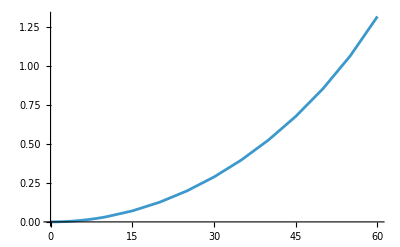

```mathematica
list1={{0.1,5.980068304801726*^-7},{1.1,5.980291466763381*^-7},{2.1,5.980886639847108*^-7},{3.1,5.981854027505376*^-7},{4.1,5.983193961031363*^-7},{5.1,5.984906900540216*^-7},{6.1,5.986993436338717*^-7},{7.1,5.989454290694144*^-7},{8.1,5.992290320016414*^-7},{9.1,5.995502517470958*^-7},{10.1,5.999092016043538*^-7},{15,6.02218174893492*^-7},{20,6.055332686532762*^-7},{25,6.098497609814151*^-7},{30,6.152149255761659*^-7},{35,6.216958248289661*^-7},{40,6.293885557034301*^-7},{45,6.384347743800003*^-7},{50,6.490530046522801*^-7},{55,6.616027863287685*^-7},{60,6.767311221020999*^-7}};

len=Length[list1];
x=5.980066445182726*^-7;
rat4=100;
scale=1/x;
dat4=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]];
ListLinePlot[%]
```

### set 2

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat1=0.5;
val1=2;val2=rat1 val1;
sig0[mu,vfval,cqval,val1,val2]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

```mathematica
list1={{0.1,0.00018000027564770522},{1.1,0.00018003335456505658},{2.1,0.00018012157658013083},{3.1,0.0001802649732644795},{4.1,0.00018046359598529915},{5.1,0.00018071751599633607},{6.1,0.00018102682456432978},{7.1,0.00018139163313155522},{8.1,0.00018181207351519307},{9.1,0.00018228829814442184},{10.1,0.0001828204803363118},{15,0.0001862442135060546},{20,0.00019116051565242983},{25,0.0001975612277830695},{30,0.0002055115160685242},{35,0.0002150978349630456},{40,0.00022643348992562156},{45,0.00023966716095087578},{50,0.0002549965051526939},{55,0.00027269130610617934},{60,0.00029313697355888666}};

len=Length[list1];
x=0.00017999999999999993;
rat1=0.5;
scale=1/x;
dat5=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat2=1;
val1=2;val2=rat2 val1;
sig0[mu,vfval,cqval,val1,val2]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

```mathematica
list1={{0.1,0.00011250009878155817},{1.1,0.00011251195307739316},{2.1,0.00011254356946882711},{3.1,0.00011259496142771957},{4.1,0.00011266615087834748},{5.1,0.00011275716824401799},{6.1,0.00011286805251195142},{7.1,0.00011299885131676843},{8.1,0.00011314962104301546},{9.1,0.00011332042694726359},{10.1,0.00011351134330042574},{15,0.0001147406118947501},{20,0.00011650897110926524},{25,0.000118817133874042},{30,0.00012169383993589452},{35,0.00012517788018499154},{40,0.00012932122402009566},{45,0.0001341939779524091},{50,0.00013989261263063266},{55,0.00014655457587881343},{60,0.00015438702696485168}};

len=Length[list1];
x=0.0001125;
rat2=1;
scale=1/x;
dat6=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat3=2;
val1=2;val2=rat3 val1;
sig0[mu,vfval,cqval,val1,val2]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

```mathematica
list1={{0.1,0.00006428575131185575},{1.1,0.00006429019464683841},{2.1,0.00006430204546087818},{3.1,0.00006432130899699452},{4.1,0.00006434799378950587},{5.1,0.00006438211168470712},{6.1,0.00006442367786967327},{7.1,0.0000644727109093586},{8.1,0.0000645292327922115},{9.1,0.00006459326898457701},{10.1,0.00006466484849421573},{15,0.00006512583299270863},{20,0.00006578930829233849},{25,0.0000666559743823932},{30,0.0000677373387444779},{35,0.00006904917556517795},{40,0.00007061305072835455},{45,0.00007245882669453557},{50,0.0000746289894559814},{55,0.00007718668546400342},{60,0.00008023230197234214}};

len=Length[list1];
x=0.00006428571428571426;
rat3=2;
scale=1/x;
dat7=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat4=100;
val1=2;val2=rat4 val1;
sig0[mu,vfval,cqval,val1,val2]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

```mathematica
list1={{0.1,1.4950170762004315*^-6},{1.1,1.4950728666908457*^-6},{2.1,1.4952216599617775*^-6},{3.1,1.495463506876344*^-6},{4.1,1.495798490257841*^-6},{5.1,1.496226725135054*^-6},{6.1,1.496748359084679*^-6},{7.1,1.4973635726735359*^-6},{8.1,1.4980725800041032*^-6},{9.1,1.4988756293677395*^-6},{10.1,1.4997730040108843*^-6},{15,1.50554543723373*^-6},{20,1.5138331716331901*^-6},{25,1.5246244024535376*^-6},{30,1.5380373139404144*^-6},{35,1.5542395620724154*^-6},{40,1.5734713892585752*^-6},{45,1.5960869359500012*^-6},{50,1.6226325116307005*^-6},{55,1.6540069658219213*^-6},{60,1.6918278052552496*^-6}};

len=Length[list1];
x=1.4950166112956813*^-6;
rat4=100;
scale=1/x;
dat8=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]];
ListLinePlot[%];
```

### set 3

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat1=0.5;
val1=2;val2=rat1 val1;
sig0[mu,vfval,cqval,val1,val2]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

```mathematica
list1={{0.1,0.00002160000102656131},{1.1,0.000021600124214664657},{2.1,0.000021600452723442468},{3.1,0.000021600986572449003},{4.1,0.000021601725793465955},{5.1,0.000021602670430511923},{6.1,0.000021603820539854233},{7.1,0.00002160517619002574},{8.1,0.000021606737461843897},{9.1,0.000021608504448433668},{10.1,0.000021610477255254235},{15,0.00002162312345993152},{20,0.0000216411442251066},{25,0.000021664360150792535},{30,0.00002169280647411682},{35,0.000021726526783304947},{40,0.00002176557334491068},{45,0.00002181000750475435},{50,0.000021859900170557528},{55,0.000021915332386238795},{60,0.00002197639601022952}};

len=Length[list1];
x=0.000021599999999999976;
rat1=0.5;
scale=1/x;
dat9=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)100},{i,1,len}]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat2=1;
val1=2;val2=rat2 val1;
sig0[mu,vfval,cqval,val1,val2]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

```mathematica
list1={{0.1,0.000013500000097970619},{1.1,0.000013500011854682034},{2.1,0.000013500043208176833},{3.1,0.00001350009416463179},{4.1,0.000013500164734086638},{5.1,0.00001350025493044811},{6.1,0.000013500364771494803},{7.1,0.00001350049427888433},{8.1,0.000013500643478161264},{9.1,0.00001350081239876671},{10.1,0.000013501001074049575},{15,0.000013502212503711275},{20,0.000013503944686086128},{25,0.000013506186481175681},{30,0.000013508949109716587},{35,0.0000135122465054088},{40,0.000013516095453620196},{45,0.00001352051576205004},{50,0.000013525530467163953},{55,0.000013531166081175015},{60,0.000013537452885519498}};

len=Length[list1];
x=0.000013499999999999996;
rat2=1;
scale=1/x;
dat10=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)100},{i,1,len}]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat3=2;
val1=2;val2=rat3 val1;
sig0[mu,vfval,cqval,val1,val2]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

```mathematica
list1={{0.1,7.714285632300531*^-6},{1.1,7.71427579413245*^-6},{2.1,7.714249559522483*^-6},{3.1,7.714206929848198*^-6},{4.1,7.714147907349094*^-6},{5.1,7.714072495128167*^-6},{6.1,7.71398069715378*^-6},{7.1,7.713872518262432*^-6},{8.1,7.713747964161851*^-6},{9.1,7.71360704143466*^-6},{10.1,7.713449757542758*^-6},{15,7.712442872266896*^-6},{20,7.711012095303277*^-6},{25,7.709175841339116*^-6},{30,7.706936672709295*^-6},{35,7.70429780674409*^-6},{40,7.701263170347857*^-6},{45,7.697837467609584*^-6},{50,7.694026262220193*^-6},{55,7.689836076932429*^-6},{60,7.68527451286724*^-6}};

len=Length[list1];
x=7.714285714285709*^-6;
rat3=2;
scale=1/x;
dat11=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)100},{i,1,len}]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat4p=50;
val1=2;val2=rat4p val1;
sig0[mu,vfval,cqval,val1,val2]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

```mathematica
list1={{0.1,3.576158849437969*^-7},{1.1,3.576147934295815*^-7},{2.1,3.5761188270859524*^-7},{3.1,3.576071527360931*^-7},{4.1,3.576006034393815*^-7},{5.1,3.5759223471785467*^-7},{6.1,3.575820464430288*^-7},{7.1,3.5757003845860357*^-7},{8.1,3.575562105805238*^-7},{9.1,3.57540562597056*^-7},{10.1,3.5752309426887874*^-7},{15,3.5741117662278156*^-7},{20,3.5725187109008096*^-7},{25,3.570469466449611*^-7},{30,3.5679632758617844*^-7},{35,3.564999232247721*^-7},{40,3.561576290950276*^-7},{45,3.557693284927788*^-7},{50,3.55334894403576*^-7},{55,3.548541919005539*^-7},{60,3.54327081113609*^-7}};

len=Length[list1];
x=3.576158940397349*^-7;
rat4p=50;
scale=1/x;
dat12=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)100},{i,1,len}]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat5p=100;
val1=2;val2=rat5p val1;
sig0[mu,vfval,cqval,val1,val2]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

```mathematica
list1={{0.1,1.794019887429907*^-7},{1.1,1.7940143524320327*^-7},{2.1,1.7939995923509965*^-7},{3.1,1.7939756069503974*^-7},{4.1,1.7939423958461716*^-7},{5.1,1.7938999585067646*^-7},{6.1,1.7938482942533005*^-7},{7.1,1.7937874022598796*^-7},{8.1,1.7937172815538832*^-7},{9.1,1.793637931016341*^-7},{10.1,1.7935493493823775*^-7},{15,1.7929818123064547*^-7},{20,1.792173957104795*^-7},{25,1.7911347409742086*^-7},{30,1.7898637627750848*^-7},{35,1.7883605411891311*^-7},{40,1.7866245206455457*^-7},{45,1.7846550788583594*^-7},{50,1.7824515362865736*^-7},{55,1.7800131679151178*^-7},{60,1.7773392178634883*^-7}};

len=Length[list1];
x=1.7940199335548166*^-7;
rat5p=100;
scale=1/x;
dat13=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)100},{i,1,len}]];
ListLinePlot[%];
```

## Plots

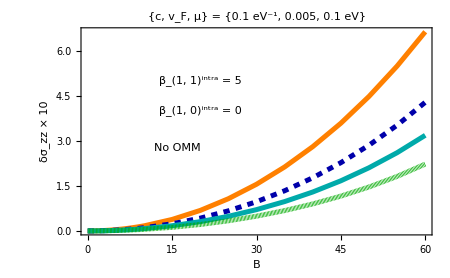
```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]]};

g1=ListPlot[{dat1,dat2,dat3,dat4},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{0,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 5",{20,5}],Darker[Brown],16,Bold],Style[Text["β_(1, 0)^intra = 0",{20,4}],Darker[Brown],16,Bold]}(*******)];
g2=-Graphics-;leg=LineLegend[style,{"0.5","1","2","100"},LabelStyle->{FontFamily->"LM Roman 10",18,Darker[Brown],Bold},LegendLayout->{"Row",1}];
pl=Legended[GraphicsGrid[{{g1},{g2}},Spacings->{0, 20},ImageSize->450],Placed[leg,Below]]
{rat1,rat2,rat3,rat4}
SetDirectory[NotebookDirectory[]];
Export["fig2a.pdf",Rasterize[pl],ImageResolution->100];
```

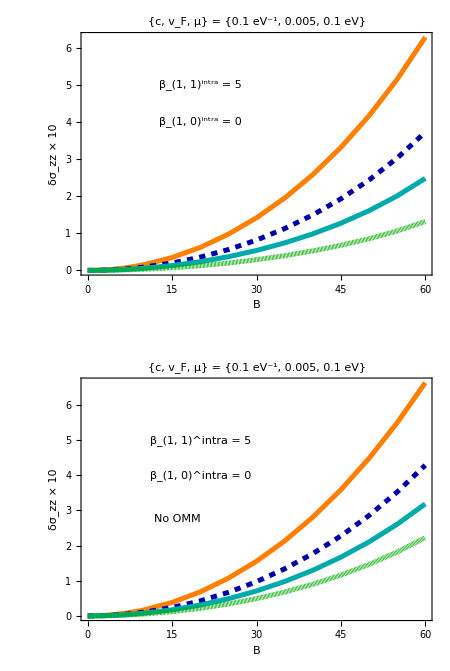

{0.5,1,2,100}

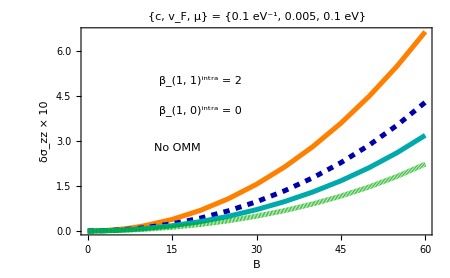
```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]]};

size=450;
g1=ListPlot[{dat5,dat6,dat7,dat8},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{0,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->size,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 2",{20,5}],Darker[Brown],16,Bold],Style[Text["β_(1, 0)^intra = 0",{20,4}],Darker[Brown],16,Bold]}(*******)];
g2=-Graphics-;leg=LineLegend[style,{"0.5","1","2","100"},LabelStyle->{FontFamily->"LM Roman 10",18,Darker[Brown],Bold},LegendLayout->{"Row",1}];
 pl=Legended[GraphicsGrid[{{g1},{g2}},Spacings->{0,20},ImageSize->450],Placed[leg,Below]]
{rat1,rat2,rat3,rat4}
SetDirectory[NotebookDirectory[]];
Export["fig2b.pdf",Rasterize[pl],ImageResolution->100];
```

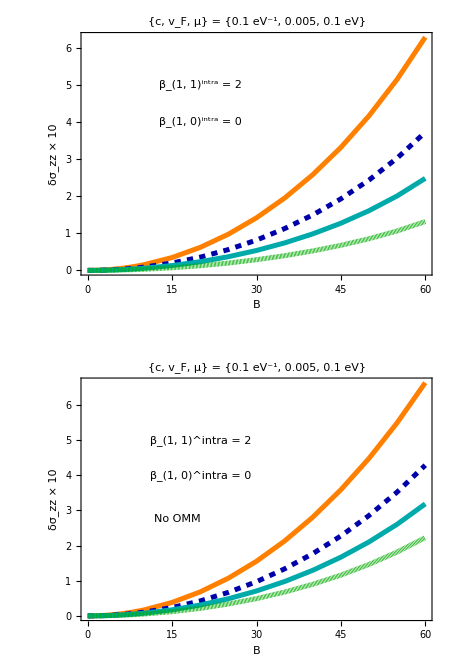

{0.5,1,2,100}

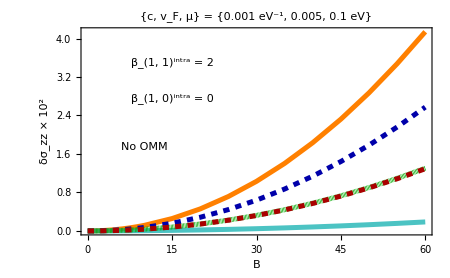
```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008],Opacity[0.7]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]],Directive[Darker[Red],Thickness[0.008],Dashing[0.01]]};

g1=ListPlot[{dat9,dat10,dat11,dat12,dat13},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{0,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10^2"},PlotLabel->Style["{c, v_F, μ} = {0.001 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 2",{15,1.5}],Darker[Brown],16,Bold],Style[Text["β_(1, 0)^intra = 0",{15,1}],Darker[Brown],16,Bold]}(*******)];

g2=-Graphics-;
(* {0.5,0.02,0.001} *)
leg=LineLegend[style,{"0.5","1","2","50","100"},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];

pl=Legended[GraphicsGrid[{{g1},{g2}},Spacings->{0, 20},ImageSize->440],Placed[leg,Below]]
{rat1,rat2,rat3,rat4p,rat5p}
SetDirectory[NotebookDirectory[]];
Export["fig2c.pdf",Rasterize[pl],ImageResolution->100];
```

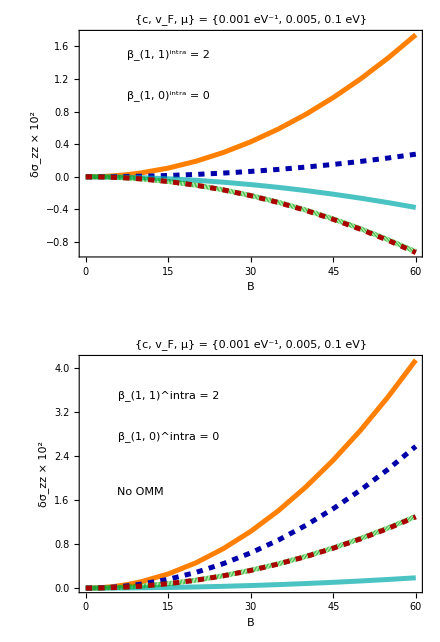

{0.5,1,2,50,100}